# 2 Body case

```mathematica
Remove["Global`*"]
$Assumptions=And@@Thread[{m1,m2,m3,s1,s2,s3,M,ρ, φ, Σ, mu12, mu312}>0]
```

m1>0&&m2>0&&m3>0&&s1>0&&s2>0&&s3>0&&M>0&&ρ>0&&φ>0&&Σ>0&&mu12>0&&mu312>0

Define the Variance and Transformation matrices

```mathematica
V = {{1/s1^2, 0},
{0, 1/s2^2}};
T={{m1/(m1 + m2), m2/(m1 + m2)},
{1, -1}};
MatrixForm[V]
MatrixForm[T]
```

(1/s1^2 | 0
0 | 1/s2^2)

(m1/(m1+m2) | m2/(m1+m2)
1 | -1)

```mathematica
Tinv = Inverse[T];
Simplify[Det[T]]
```

-1

Perform the change of variables in the exponent:

```mathematica
J = {R, r};
exp = FullSimplify[Transpose[J].Transpose[Tinv].V.Tinv.J]
```

((m1 r-(m1+m2) R)^2 s1^2+(m1 R+m2 (r+R))^2 s2^2)/((m1+m2)^2 s1^2 s2^2)

Extract the coefficients

```mathematica
alpha = Coefficient[exp, R^2] // FullSimplify
v = Coefficient[exp, R,1 ]// FullSimplify
const = Coefficient[exp, R, 0]// FullSimplify
```

1/s1^2+1/s2^2

(2 r (m2/s1^2-m1/s2^2))/(m1+m2)

(r^2 (m1^2 s1^2+m2^2 s2^2))/((m1+m2)^2 s1^2 s2^2)

Perform Gaussian integral

```mathematica
u = {u1, u2, u3};
β ={b1, b2, b3};
$Assumptions = α>0 ;
Integrate[Exp[-1/2(α u.u + u.β)], {u1, -Infinity, Infinity}, {u2, -Infinity, Infinity},{u3, -Infinity, Infinity}]
```

(2 ⅇ^((b1^2+b2^2+b3^2)/(8 α)) π √(2 π))/α^(3/2)

Result:

```mathematica
exp = -1/2 const + v^2/(8alpha) //FullSimplify
```

-r^2/(2 (s1^2+s2^2))

Compute normalization:

```mathematica
$Assumptions=s1>0&&s2>0;
N1 = (1/(Sqrt[2Pi]s1))^3;
N2 = (1/(Sqrt[2Pi]s2))^3;
norm = N1 N2 (2Pi/alpha)^(3/2) //FullSimplify
```

1/(2 √2 π^(3/2) (s1^2+s2^2)^(3/2))

```mathematica
Source2B = norm * Exp[exp];
Source2B = FullSimplify[Source2B/. (1/s1^2 + 1/s2^2)->s1^2*s2^2/(s1^2 + s2^2)^2 // PowerExpand];
Source2B = FullSimplify[Source2B/. (s1^2 + s2^2)->2r0^2]
```

(ⅇ^(-r^2/(4 r0^2)))/(8 π^(3/2) (r0^2)^(3/2))

Final result:

## Compute average radius

```mathematica
$Assumptions=r0>0;
Integrate[4 Pi r^2 * r * Source2B, {r, 0, Infinity}]
```

(4 r0)/(√π)

# 3Body case

```mathematica
Remove["Global`*"]
```

```mathematica
V = {{1/s1^2, 0, 0},
{0, 1/s2^2, 0},
{0, 0, 1/s3^2}};
T = {{m1/(m1+m2 + m3), m2/(m1+m2 + m3), m3/(m1+m2 + m3)},
{1, -1, 0},
{-m1/(m1+m2), -m2/(m1+m2), 1}};
Tinv = Simplify[Inverse[T]];
```

```mathematica
MatrixForm[V]
MatrixForm[T]
MatrixForm[Tinv]
Simplify[Det[T]]
```

(1/s1^2 | 0 | 0
0 | 1/s2^2 | 0
0 | 0 | 1/s3^2)

(m1/(m1+m2+m3) | m2/(m1+m2+m3) | m3/(m1+m2+m3)
1 | -1 | 0
-m1/(m1+m2) | -m2/(m1+m2) | 1)

(1 | m2/(m1+m2) | -m3/(m1+m2+m3)
1 | -m1/(m1+m2) | -m3/(m1+m2+m3)
1 | 0 | (m1+m2)/(m1+m2+m3))

-1

```mathematica
P = Simplify[Transpose[Tinv].V.Tinv];
MatrixForm[P]
Simplify[Det[P]]
```

(1/s1^2+1/s2^2+1/s3^2 | (m2/s1^2-m1/s2^2)/(m1+m2) | (-m3/s1^2-m3/s2^2+(m1+m2)/s3^2)/(m1+m2+m3)
(m2/s1^2-m1/s2^2)/(m1+m2) | (m2^2/s1^2+m1^2/s2^2)/(m1+m2)^2 | (m3 (m1 s1^2-m2 s2^2))/((m1+m2) (m1+m2+m3) s1^2 s2^2)
(-m3/s1^2-m3/s2^2+(m1+m2)/s3^2)/(m1+m2+m3) | (m3 (m1 s1^2-m2 s2^2))/((m1+m2) (m1+m2+m3) s1^2 s2^2) | (m3^2 (1/s1^2+1/s2^2)+(m1+m2)^2/s3^2)/(m1+m2+m3)^2)

1/(s1^2 s2^2 s3^2)

```mathematica
J = {R, r12, r312};
expr = Simplify[Transpose[J].P.J]
lim = Limit[expr, m3-> 0 ]
```

(2 R r12 (m2/s1^2-m1/s2^2))/(m1+m2)+(r12^2 (m2^2/s1^2+m1^2/s2^2))/(m1+m2)^2+(2 m3 r12 r312 (m1 s1^2-m2 s2^2))/((m1+m2) (m1+m2+m3) s1^2 s2^2)+R^2 (1/s1^2+1/s2^2+1/s3^2)+(2 R r312 (-m3/s1^2-m3/s2^2+(m1+m2)/s3^2))/(m1+m2+m3)+(r312^2 (m3^2 (1/s1^2+1/s2^2)+(m1+m2)^2/s3^2))/(m1+m2+m3)^2

(2 R r12 (m2/s1^2-m1/s2^2))/(m1+m2)+(r12^2 (m2^2/s1^2+m1^2/s2^2))/(m1+m2)^2+R^2 (1/s1^2+1/s2^2+1/s3^2)+(2 R r312)/s3^2+r312^2/s3^2

```mathematica
Coefficient[lim, r12]// FullSimplify
```

(2 R (m2/s1^2-m1/s2^2))/(m1+m2)

```mathematica
alpha = Coefficient[expr, R, 2]
v = Coefficient[expr, R, 1]
const = Coefficient[expr, R, 0]
FullSimplify[expr- alpha*R^2 - v*R - const]
```

1/s1^2+1/s2^2+1/s3^2

(2 r12 (m2/s1^2-m1/s2^2))/(m1+m2)+(2 r312 (-m3/s1^2-m3/s2^2+(m1+m2)/s3^2))/(m1+m2+m3)

(r12^2 (m2^2/s1^2+m1^2/s2^2))/(m1+m2)^2+(2 m3 r12 r312 (m1 s1^2-m2 s2^2))/((m1+m2) (m1+m2+m3) s1^2 s2^2)+(r312^2 (m3^2 (1/s1^2+1/s2^2)+(m1+m2)^2/s3^2))/(m1+m2+m3)^2

0

```mathematica
$Assumptions=s1>0&&s2>0 &&s3>0;
N1= (1/(Sqrt[2*Pi]*s1))^3;
N2= (1/(Sqrt[2*Pi]*s2))^3;
N3= (1/(Sqrt[2*Pi]*s3))^3;
norm = N1 N2 N3 (2 Pi / alpha)^(3/2) // FullSimplify
```

1/(8 π^3 (s2^2 s3^2+s1^2 (s2^2+s3^2))^(3/2))

```mathematica
Limit[Limit[norm, s2->s1], s3->s1]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/(24 √3 π^3 s1^6)

```mathematica
$Assumptions=m1>0&&m2>0 &&m3 >0 && s1>0&&s2>0 && s3 >0;
exp = -1/2 * const + v^2/(8 alpha)
```

1/2 (-(r12^2 (m2^2/s1^2+m1^2/s2^2))/(m1+m2)^2-(2 m3 r12 r312 (m1 s1^2-m2 s2^2))/((m1+m2) (m1+m2+m3) s1^2 s2^2)-(r312^2 (m3^2 (1/s1^2+1/s2^2)+(m1+m2)^2/s3^2))/(m1+m2+m3)^2)+(((2 r12 (m2/s1^2-m1/s2^2))/(m1+m2)+(2 r312 (-m3/s1^2-m3/s2^2+(m1+m2)/s3^2))/(m1+m2+m3))^2)/(8 (1/s1^2+1/s2^2+1/s3^2))

```mathematica
lim1 =Limit[exp, m2->m1]
lim2 =Limit[lim1, m3->m1] 
lim2 =Limit[lim2, s2->s1] 
lim2 =Limit[lim2, s3->s1]  // FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/2 (-(r12^2 (m1^2/s1^2+m1^2/s2^2))/(4 m1^2)-(m3 r12 r312 (m1 s1^2-m1 s2^2))/(m1 (2 m1+m3) s1^2 s2^2)-(r312^2 (m3^2 (1/s1^2+1/s2^2)+(4 m1^2)/s3^2))/(2 m1+m3)^2)+(((r12 (m1/s1^2-m1/s2^2))/m1+(2 r312 (-m3/s1^2-m3/s2^2+(2 m1)/s3^2))/(2 m1+m3))^2)/(8 (1/s1^2+1/s2^2+1/s3^2))

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/2 (-(r12^2 (m1^2/s1^2+m1^2/s2^2))/(4 m1^2)-(r12 r312 (m1 s1^2-m1 s2^2))/(3 m1 s1^2 s2^2)-(r312^2 (m1^2 (1/s1^2+1/s2^2)+(4 m1^2)/s3^2))/(9 m1^2))+(((r12 (m1/s1^2-m1/s2^2))/m1+(2 r312 (-m1/s1^2-m1/s2^2+(2 m1)/s3^2))/(3 m1))^2)/(8 (1/s1^2+1/s2^2+1/s3^2))

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/2 (-r12^2/(2 s1^2)-(r312^2 ((2 m1^2)/s1^2+(4 m1^2)/s3^2))/(9 m1^2))+(r312^2 (-(2 m1)/s1^2+(2 m1)/s3^2)^2)/(18 m1^2 (2/s1^2+1/s3^2))

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

-(3 r12^2+4 r312^2)/(12 s1^2)

```mathematica
Limit[exp, s3 ->Infinity] // FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

-r12^2/(2 (s1^2+s2^2))

```mathematica
aa = Coefficient[exp, r12, 2] 
ab = Coefficient[exp, r12 r312, 1]  //FullSimplify
bb = Coefficient[exp, r312, 2] // FullSimplify
FullSimplify[exp - aa * r12^2 - ab * r12*r312 - bb*r312^2]
```

-m2^2/(2 (m1+m2)^2 s1^2)-m1^2/(2 (m1+m2)^2 s2^2)+m2^2/(2 (m1+m2)^2 s1^4 (1/s1^2+1/s2^2+1/s3^2))+m1^2/(2 (m1+m2)^2 s2^4 (1/s1^2+1/s2^2+1/s3^2))-(m1 m2)/((m1+m2)^2 s1^2 s2^2 (1/s1^2+1/s2^2+1/s3^2))

(-m1 s1^2+m2 s2^2)/((m1+m2) (s2^2 s3^2+s1^2 (s2^2+s3^2)))

-(s1^2+s2^2)/(2 (s2^2 s3^2+s1^2 (s2^2+s3^2)))

0

```mathematica
Limit[aa, s3->Infinity]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(-m1^2 s1^2 s2^2-2 m1 m2 s1^2 s2^2-m2^2 s1^2 s2^2)/(2 m1^2 s1^4 s2^2+4 m1 m2 s1^4 s2^2+2 m2^2 s1^4 s2^2+2 m1^2 s1^2 s2^4+4 m1 m2 s1^2 s2^4+2 m2^2 s1^2 s2^4)

```mathematica
-(m2^2/(2 (m1+m2)^2 s1^2))[1-1/(s1^2 (1/s1^2+1/s2^2+1/s3^2))]-(m1^2/(2 (m1+m2)^2 s2^2))[1-1/(s2^2 (1/s1^2+1/s2^2+1/s3^2))]-(m1 m2)/((m1+m2)^2 s1^2 s2^2 (1/s1^2+1/s2^2+1/s3^2))
```

-(m1 m2)/((m1+m2)^2 s1^2 s2^2 (1/s1^2+1/s2^2+1/s3^2))-m2^2/(2 (m1+m2)^2 s1^2)[1-1/(s1^2 (1/s1^2+1/s2^2+1/s3^2))]-m1^2/(2 (m1+m2)^2 s2^2)[1-1/(s2^2 (1/s1^2+1/s2^2+1/s3^2))]

Check the normalization

```mathematica
GaussianIntegral3D[α_, v_, c_]:=(2Pi/α)^(3/2)*Exp[-1/2 c + v^2/(8α)]
```

```mathematica
integrand = GaussianIntegral3D[-2 *bb, -2 ab*r12, -2 aa * r12*r12 ] // FullSimplify //ExpandAll //FullSimplify
```

2 √2 ⅇ^(-r12^2/(2 (s1^2+s2^2))) π^(3/2) ((s1^2 s2^2)/(s1^2+s2^2)+s3^2)^(3/2)

```mathematica
4Pi norm Integrate[r12^2 integrand, {r12, 0, Infinity}]
```

1

## The 3B source in JC

```mathematica
Source = norm * Exp[exp]
```

(ⅇ^(1/2 (-(r12^2 (m2^2/s1^2+m1^2/s2^2))/(m1+m2)^2-(2 m3 r12 r312 (m1 s1^2-m2 s2^2))/((m1+m2) (m1+m2+m3) s1^2 s2^2)-(r312^2 (m3^2 (1/s1^2+1/s2^2)+(m1+m2)^2/s3^2))/(m1+m2+m3)^2)+(((2 r12 (m2/s1^2-m1/s2^2))/(m1+m2)+(2 r312 (-m3/s1^2-m3/s2^2+(m1+m2)/s3^2))/(m1+m2+m3))^2)/(8 (1/s1^2+1/s2^2+1/s3^2))))/(8 π^3 (s2^2 s3^2+s1^2 (s2^2+s3^2))^(3/2))

### Source for AAA in JC

```mathematica
SourceAAAJC = Source /.m1-> m /.m2->m /.m3->m /.s1->s /. s2->s /.s3->s // FullSimplify
$Assumptions=m>0&&s>0;
Integrate[r12^2 r312^2 SourceAAAJC, {r12, 0, Infinity}, {r312, 0, Infinity}] * 4 * Pi * 4 * Pi
```

(ⅇ^(-(3 r12^2+4 r312^2)/(12 s^2)))/(24 √3 π^3 (s^4)^(3/2))

1

## Move to hyperspherical coordinates

ⅇ^(1/2 (-(r12^2 (m2^2/s1^2+m1^2/s2^2))/(m1+m2)^2-(2 m3 r12 r312 (m1 s1^2-m2 s2^2))/((m1+m2) (m1+m2+m3) s1^2 s2^2)-(r312^2 (m3^2 (1/s1^2+1/s2^2)+(m1+m2)^2/s3^2))/(m1+m2+m3)^2)+(((2 r12 (m2/s1^2-m1/s2^2))/(m1+m2)+(2 r312 (-m3/s1^2-m3/s2^2+(m1+m2)/s3^2))/(m1+m2+m3))^2)/(8 (1/s1^2+1/s2^2+1/s3^2)))/(8 π^3 (s2^2 s3^2+s1^2 (s2^2+s3^2))^(3/2))

In the  exponent there are 3 terms: 1 quadratic in , one quadratic in and one that depends on the scalar product .
From the definitions of the hyperspherical coordinates:

and

To compute the scalar product in spherical coordinates define  and

```mathematica
v1 = {r1 Sin[theta1] Cos[phi1] , r1 Sin[theta1]Sin[phi1] , r1 Cos[theta1]};
v2 = {r2 Sin[theta2] Cos[phi2] , r2 Sin[theta2]Sin[phi2] , r2 Cos[theta2]};
```

```mathematica
v1.v2 // FullSimplify// TrigReduce // FullSimplify
```

r1 r2 (Cos[theta1] Cos[theta2]+Cos[phi1-phi2] Sin[theta1] Sin[theta2])

```mathematica
Clear[r12, r312]
C12 = Coefficient[exp, r12 ^2] // FullSimplify
C312 = Coefficient[exp, r312, 2] // FullSimplify
CScalar = (exp - C12 * r12^2 - C312 * r312^2)/r12 / r312 // FullSimplify
```

-(m1^2 s1^2+m2^2 s2^2+(m1+m2)^2 s3^2)/(2 (m1+m2)^2 (s2^2 s3^2+s1^2 (s2^2+s3^2)))

-(s1^2+s2^2)/(2 (s2^2 s3^2+s1^2 (s2^2+s3^2)))

(-m1 s1^2+m2 s2^2)/((m1+m2) (s2^2 s3^2+s1^2 (s2^2+s3^2)))

```mathematica
r12 = Sqrt[M/mu12]ρ Cos[φ];
r312 = Sqrt[M/mu312]ρ Sin[φ];
```

```mathematica
mu12 = m1 m2 /(m1 + m2);
mu312 = m3(m1 + m2)/(m1 +m2+m3);
E12 = C12 * M/mu12 ρ^2 Cos[φ]^2
E312 =C312 *  M/mu312 ρ^2 Sin[φ]^2
EPart = CScalar *M/Sqrt[mu12 * mu312]ρ^ 2 Cos[φ]Sin[φ] (Cos[theta1] Cos[theta2]+Cos[phi1-phi2] Sin[theta1] Sin[theta2])
```

-(M (m1^2 s1^2+m2^2 s2^2+(m1+m2)^2 s3^2) ρ^2 Cos[φ]^2)/(2 m1 m2 (m1+m2) (s2^2 s3^2+s1^2 (s2^2+s3^2)))

-(M (m1+m2+m3) (s1^2+s2^2) ρ^2 Sin[φ]^2)/(2 (m1+m2) m3 (s2^2 s3^2+s1^2 (s2^2+s3^2)))

(M (-m1 s1^2+m2 s2^2) ρ^2 Cos[φ] (Cos[theta1] Cos[theta2]+Cos[phi1-phi2] Sin[theta1] Sin[theta2]) Sin[φ])/((m1+m2) √((m1 m2 m3)/(m1+m2+m3)) (s2^2 s3^2+s1^2 (s2^2+s3^2)))

```mathematica
.b4
```

.b4

Compute the general source.
The infinitesimal volume element is

```mathematica
SourceHC = M^3/(mu12 mu312)^(3/2)norm * Exp[Collect[Collect[E12 + E312 + EPart, (M ρ^2/(m1 +m2))], 1/ (s2^2 s3^2+s1^2 (s2^2+s3^2))]](* keep ρ^5 separate *)
```

(ⅇ^(1/((m1+m2) (s2^2 s3^2+s1^2 (s2^2+s3^2)))M ρ^2 (-((m1^2 s1^2+m2^2 s2^2+(m1+m2)^2 s3^2) Cos[φ]^2)/(2 m1 m2)+((-m1 s1^2+m2 s2^2) Cos[φ] (Cos[theta1] Cos[theta2]+Cos[phi1-phi2] Sin[theta1] Sin[theta2]) Sin[φ])/(√((m1 m2 m3)/(m1+m2+m3)))-((m1+m2+m3) (s1^2+s2^2) Sin[φ]^2)/(2 m3))) M^3)/(8 ((m1 m2 m3)/(m1+m2+m3))^(3/2) π^3 (s2^2 s3^2+s1^2 (s2^2+s3^2))^(3/2))

Compute the solid hyperangle:

```mathematica
Integrate[Sin[phi]^2Cos[phi]^2, {phi, 0, Pi/2}] * Integrate[1, {dcost12, -1, 1}]*Integrate[1, {dcost312, -1, 1}]Integrate[1, {dphi12, 0, 2Pi}]Integrate[1, {dphi312, 0, 2Pi}]
```

π^3

## Check source for m1 = m2 = m3 = m (ppp case)

```mathematica
(* Pi^3 comes from integration of dΩ *)
Sourceppp = SourceHC/.m1->m/.m2->m/.m3->m/.s1->s/.s2->s/.s3->s /.s->Sqrt[M/(2m)]rho0// FullSimplify //PowerExpand
```

(ⅇ^(-ρ^2/rho0^2))/(π^3 rho0^6)

```mathematica
Sourceeee =Pi^3 SourceHC/.m1->m/.m2->m/.m3->m/.s1->s/.s2->s/.s3->s// FullSimplify //PowerExpand
```

(ⅇ^(-(M ρ^2)/(2 m s^2)) M^3)/(8 m^3 s^6)

```mathematica
$Assumptions=rho0>0;
(* factor ρ^5 comes from jacobian of hyperspherical coord. transformation *)
Integrate[Sourceppp * ρ^5, {ρ, 0, Infinity}] * Pi^3
```

1

### Average source

```mathematica
Integrate[Pi^3 * ρ^5 * ρ * Sourceppp , {ρ, 0, Infinity}]
```

(15 √π rho0)/16

### ppp Source with resonances

```mathematica
SourcePdfHC = SourceHC * ρ^5* Pi^3
```

(ⅇ^(1/((m1+m2) (s2^2 s3^2+s1^2 (s2^2+s3^2)))M ρ^2 (-((m1^2 s1^2+m2^2 s2^2+(m1+m2)^2 s3^2) Cos[φ]^2)/(2 m1 m2)+((-m1 s1^2+m2 s2^2) Cos[φ] (Cos[theta1] Cos[theta2]+Cos[phi1-phi2] Sin[theta1] Sin[theta2]) Sin[φ])/(√((m1 m2 m3)/(m1+m2+m3)))-((m1+m2+m3) (s1^2+s2^2) Sin[φ]^2)/(2 m3))) M^3 ρ^5)/(8 ((m1 m2 m3)/(m1+m2+m3))^(3/2) (s2^2 s3^2+s1^2 (s2^2+s3^2))^(3/2))

```mathematica
$Assumptions = m> 0 && sp > 0 && ss > 0;
SourcePdfAAA = SourcePdfHC /.m1->m/.m2->m/.m3->m/.M-> m/2;
SourcePdfAAAppp = SourcePdfAAA /.s1->sp/.s2->sp/.s3->sp //FullSimplify
SourcePdfAAApps = SourcePdfAAA Integrate[1, {dcost12, -1, 1}]*Integrate[1, {dcost312, -1, 1}]Integrate[1, {dphi12, 0, 2Pi}]Integrate[1, {dphi312, 0, 2Pi}]/ Pi^3* Sin[φ]^2Cos[φ]^2/.s1->sp/.s2->sp/.s3->ss // FullSimplify
SourcePdfAAApss = SourcePdfAAA /.s1->ss/.s2->ss/.s3->sp // FullSimplify
SourcePdfAAAsss = SourcePdfAAA /.s1->ss/.s2->ss/.s3->ss // FullSimplify
```

(ⅇ^(-ρ^2/(4 sp^2)) ρ^5)/(64 sp^6)

(3 √3 ⅇ^(1/4 ρ^2 (-Cos[φ]^2/sp^2-(3 Sin[φ]^2)/(sp^2+2 ss^2))) ρ^5 Cos[φ]^2 Sin[φ]^2)/(4 π sp^3 (sp^2+2 ss^2)^(3/2))

(3 √3 ⅇ^(-(ρ^2 (sp^2+2 ss^2+(sp-ss) (sp+ss) Cos[2 φ]))/(4 ss^2 (2 sp^2+ss^2))) ρ^5)/(64 ss^3 (2 sp^2+ss^2)^(3/2))

(ⅇ^(-ρ^2/(4 ss^2)) ρ^5)/(64 ss^6)

```mathematica
SourcePdfAAApps/. sp-> 1/.ss->2/.M->m/2/.m->1
```

(ⅇ^(1/4 ρ^2 (-Cos[φ]^2-Sin[φ]^2/3)) ρ^5)/(192 √3)

```mathematica
Integrate[SourcePdfAAAppp, {ρ, 0, Infinity}]
$Assumptions = ss > sp &&sp >0 && ss >0
Integrate[SourcePdfAAApps, {φ, 0, Pi/2}, {ρ, 0, Infinity}]
```

1

ss>sp&&sp>0&&ss>0

1

(ⅇ^(-ρ^2/4) ρ^5)/(192 √3)

(ⅇ^(-ρ^2/12) ρ^5)/(192 √3)

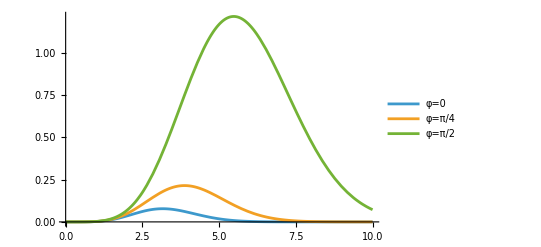

```mathematica
SourcePdfAAApps/. sp-> 1/.ss->2/.M->m/2/. φ-> 0
SourcePdfAAApps/. sp-> 1/.ss->2/.M->m/2/. φ-> Pi/2
Plot[{SourcePdfAAApps/. sp-> 1/.ss->2/.M->m/2/. φ-> 0, SourcePdfAAApps/. sp-> 1/.ss->2/.M->m/2/.m->1/. φ-> Pi/4,  SourcePdfAAApps/. sp-> 1/.ss->2/.M->m/2/.m->1/. φ-> Pi/2},  {ρ, 0,10}, PlotLegends->{"φ=0", "φ=π/4","φ=π/2"}]
```

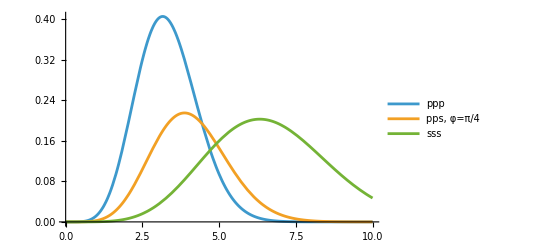

```mathematica
Plot[{SourcePdfAAAppp/. sp-> 1/.M->m/2, SourcePdfAAApps/. sp-> 1/.ss->2/.M->m/2/.m->1/. φ-> Pi/4,  SourcePdfAAAsss/. ss->2/.M->m/2},  {ρ, 0,10}, PlotLegends->{"ppp", "pps, φ=π/4","sss"}]
```

## Compute the source function for AAB systems

```mathematica
sourceAAB = SourceHC* Integrate[1, {dcost12, -1, 1}]*Integrate[1, {dcost312, -1, 1}]Integrate[1, {dphi12, 0, 2Pi}]Integrate[1, {dphi312, 0, 2Pi}] /.m1->m /. m2->m /.s1->s/.s2->s
```

(2 ⅇ^((M ρ^2 (-((2 m^2 s^2+4 m^2 s3^2) Cos[φ]^2)/(2 m^2)-((2 m+m3) s^2 Sin[φ]^2)/m3))/(2 m (s^2 s3^2+s^2 (s^2+s3^2)))) M^3)/(((m^2 m3)/(2 m+m3))^(3/2) π (s^2 s3^2+s^2 (s^2+s3^2))^(3/2))

#### Source for AAB systems averaged over the hyper-angle

```mathematica
sourceAABAvgPhi = Integrate[Sin[φ]^2*Cos[φ]^2 sourceAAB,  {φ, 0, Pi/2}] //FullSimplify
```

(ⅇ^(-(M ((m+m3) s^2+m3 s3^2) ρ^2)/(2 m m3 s^2 (s^2+2 s3^2))) M^3 Hypergeometric0F1Regularized[2,((m M s^2 ρ^2-M m3 s3^2 ρ^2)^2)/(4 (2 m m3 s^4+4 m m3 s^2 s3^2)^2)])/(8 m^3 (m3/(2 m+m3))^(3/2) (s^4+2 s^2 s3^2)^(3/2))

```mathematica
$Assumptions= m>0&& s>0;
sourceAABAvgPhi/. M->m/2 /. m3->m /. s3->s//FullSimplify
```

(ⅇ^(-ρ^2/(4 s^2)))/(64 s^6)

```mathematica
Integrate[(ⅇ^(-ρ^2/(4 s^2)))/(64 s^6)*ρ^5 ,  {ρ, 0, Infinity}]
```

1

```mathematica
$Assumptions= m>0&& s>0 && s3>0 && M>0 && m3>0
Integrate[sourceAABAvgPhi * ρ^5 ,  {ρ, 0, Infinity}]
```

m>0&&s>0&&s3>0&&M>0&&m3>0

1

```mathematica
Coefficient[E12, ρ^2*Cos[φ]^2]
```

-(M (m1^2 s1^2+m2^2 s2^2+(m1+m2)^2 s3^2))/(2 m1 m2 (m1+m2) (s2^2 s3^2+s1^2 (s2^2+s3^2)))

```mathematica
Coefficient[E312, ρ^2Sin[φ]^2]/Coefficient[E12, ρ^2*Cos[φ]^2] -1 /.m2->m1 /.s2->s1//FullSimplify
```

-1+((2 m1+m3) s1^2)/(m3 (s1^2+2 s3^2))

```mathematica
Coefficient[EPart, ρ^2Cos[φ]Sin[φ](Cos[theta1] Cos[theta2]+Cos[phi1-phi2] Sin[theta1] Sin[theta2]) ]/Coefficient[E12, ρ^2*Cos[φ]^2] // Simplify
```

-(2 m1 m2 (-m1 s1^2+m2 s2^2))/(√((m1 m2 m3)/(m1+m2+m3)) (m1^2 s1^2+m2^2 s2^2+(m1+m2)^2 s3^2))